Proposed dimension measures

```mathematica
CalculateNodeShellDistance[n_,k_,g_]:=Module[{NodeCloud},NodeCloud=Split[Sort[GraphDistanceMatrix[g] [[n]]]];Log[Length[NodeCloud[[k]]]]/Log[k]+1];
```

Takes the vertex degree of the vertices on k-graph periphery of a network. The asymptotic version starts from the center towards the boundaries.

```mathematica
KShellBoundary[g_]:=Module[{diam=GraphDiameter[UndirectedGraph[g]],std=N@StandardDeviation[Flatten@GraphDistanceMatrix[UndirectedGraph[g]]]},DeleteDuplicates[First/@Position[GraphDistanceMatrix[UndirectedGraph[g]],x_/;x≥diam-(.5 std)]]]
```

```mathematica
KShellBoundary[g_,m_]:=Module[{diam=GraphDiameter[UndirectedGraph[g]],std=N@StandardDeviation[Flatten@GraphDistanceMatrix[UndirectedGraph[g]]]},DeleteDuplicates[First/@Position[GraphDistanceMatrix[UndirectedGraph[g]],x_/;x≥diam-(m std)]]]
```

```mathematica
ShellDimension[g_]:=Module[{rg=AdjacencyGraph[AdjacencyMatrix[g]]},Median[VertexDegree[UndirectedGraph@rg,#]&/@KShellBoundary[g]]]
```

```mathematica
AssymptoticShellDimension[g_]:=Module[{rg=AdjacencyGraph[AdjacencyMatrix[g]]},Module[{diam=GraphDiameter[UndirectedGraph@rg]},Reverse@Table[Mean[VertexDegree[UndirectedGraph@rg,#]&/@KShellBoundary[rg,m]],{m,0,diam,.5}]]]
```

n allows to reduce the computation, e.g. n = 2 by 2

```mathematica
AssymptoticShellDimension[g_,n_:1]:=Module[{rg=AdjacencyGraph[AdjacencyMatrix[g]]},Module[{diam=GraphDiameter[UndirectedGraph@rg]},Reverse@Table[Mean[VertexDegree[UndirectedGraph@rg,#]&/@KShellBoundary[rg,m]],{m,0,diam/n,.5}]]]
```

```mathematica
ShellDimension[-Graphics-]
```

2

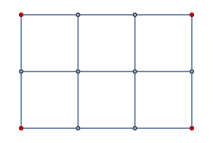

```mathematica
HighlightGraph[-Graphics-,Subgraph[-Graphics-,KShellBoundary[-Graphics-]]]
```

```mathematica
N/@AssymptoticShellDimension[-Graphics-]
```

{2.83333,2.83333,2.83333,2.83333,2.83333,2.83333,2.83333,2.6,2.6,2.,2.}

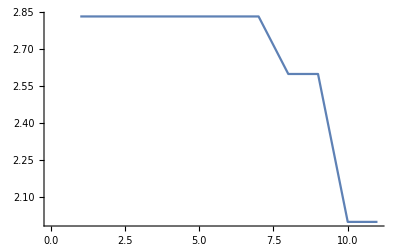

```mathematica
ListLinePlot[N/@AssymptoticShellDimension[-Graphics-]]
```

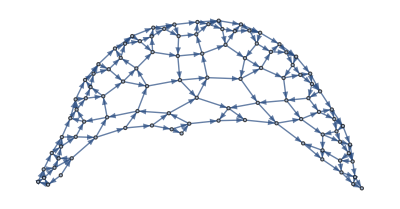
```mathematica
HighlightGraph[-Graphics-,Subgraph[-Graphics-,KShellBoundary[-Graphics-]]]
```

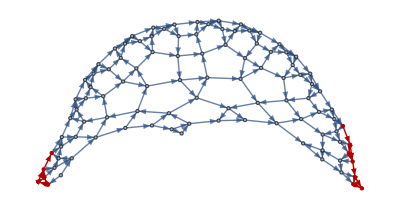

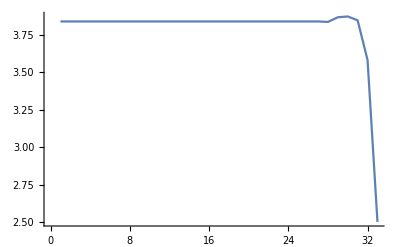

```mathematica
ListLinePlot[N/@AssymptoticShellDimension[-Graphics-]]
```

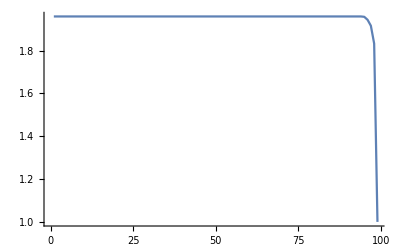

```mathematica
ListLinePlot[N/@AssymptoticShellDimension[PathGraph[Range[50]]]]
```

```mathematica
Last@AssymptoticShellDimension[PathGraph[Range[50]]]
```

1

```mathematica
N@Last@AssymptoticShellDimension[-Graphics-]
```

2.5

```mathematica
N@Last@AssymptoticShellDimension[-Graphics-]
```

2.

```mathematica
ShellDimension[GridGraph[{3,3,7}]]
```

3

```mathematica
N@Last@AssymptoticShellDimension[GridGraph[{3,5,3}]]
```

3.

```mathematica
N@Last@AssymptoticShellDimension[GridGraph[{3,3,3,3,2}]]
```

5.

```mathematica
N@Last@AssymptoticShellDimension[GridGraph[{2,2,2,2,2,2}]]
```

6.

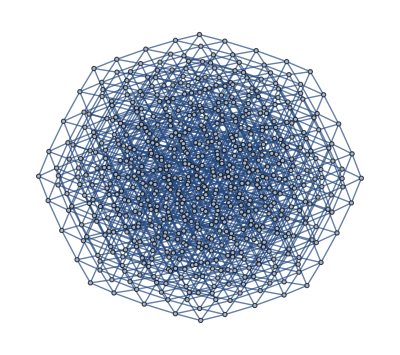

```mathematica
g=GridGraph[{5,5,5,5}]
```

```mathematica
N/@Table[CalculateNodeShellDistance[SortBy[Thread[{EdgeList[g],EdgeBetweennessCentrality[g]}],Last][[-1]][[1,1]],i,g],{i,2,13}]
```

```mathematica
GetHD[g_]:=Module[{gdm,centraledge,n,vc,gcs},gdm=GraphDistanceMatrix[UndirectedGraph[g]];
n=1;
vc=VertexCount[g];gcs=GraphCenter[UndirectedGraph[g]];
centraledge=gcs[[Ceiling[Length[gcs]/2]]];
While[Length[Select[gdm[[centraledge]],#≤n&]]<vc/2,n=n;
n++];Log[n,Length[Select[gdm[[centraledge]],#≤n&]]]]

csarray=Table[GridGraph[{i,i}],{i,1,100}];

GetHD[csarray[[Length[csarray]]]]//N
```

2.1822

```mathematica
dimvalues2=Table[Table[Last[AssymptoticShellDimension[#,2]&@AdjacencyGraph[Last@CreateTruningCSTimeSeries[m,8,2,t]]],{m,randTMs2}],{t,{20,30,50}}];
```

```mathematica
dimvalues3=Table[Table[N@GetHD[#]&@AdjacencyGraph[Last@CreateTruningCSTimeSeries[m,8,2,t]],{m,randTMs2}],{t,{20,30,50}}];
```

```mathematica
dimvalues4=Table[Table[N@Median@DimensionList[#]&@AdjacencyGraph[Last@CreateTruningCSTimeSeries[m,8,2,t]],{m,randTMs2}],{t,{20,30,50}}];
```

```mathematica
curvatures=Table[Table[N@Median@Curvatures[#]&@AdjacencyGraph[Last@CreateTruningCSTimeSeries[m,8,2,t]],{m,randTMs2}],{t,{20,30,50}}];
```

```mathematica
randTMs2=RandomInteger[{0,1645074-1},100];
```

```mathematica
dimvalues2b=Table[Last[AssymptoticShellDimension[#,2]&@Last@CreateCSSeriesTrinetReplacement[m,50]],{m,randTMs2}];
```

```mathematica
dimvalues3b=Table[N@GetHD[#]&@Last@CreateCSSeriesTrinetReplacement[m,50],{m,randTMs2}];
```

```mathematica
randTMs2[[1]]
```

252920

```mathematica
graphs=Last/@(CreateCSSeriesTrinetReplacement[#,50]&/@randTMs2);
```

```mathematica
Table[N@Median@DimensionList[#]&@AdjacencyGraph[Last@CreateTruningCSTimeSeries[m,8,2,t]],{m,randTMs2}]
```

```mathematica
dimvalues4b=(Dimension/@graphs);
```

```mathematica
curvaturesb=N/@Median/@(Curvatures/@graphs);
```

### TMs model

This dimension and curvature distributions are very stable for TM generated causal nets.

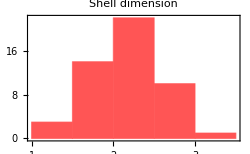
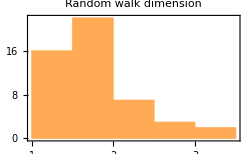

```mathematica
Row[{Histogram[dimvalues2[[3]],PlotTheme->"Web",ChartStyle->Lighter[Red],ImageSize->250,PlotLabel->"Shell dimension"],"    ",Histogram[dimvalues3[[3]],PlotTheme->"Web",ChartStyle->Lighter[Orange],ImageSize->250,PlotLabel->"Random walk dimension"]}]
```

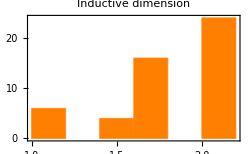
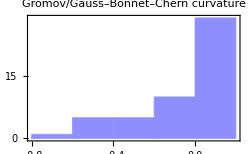

```mathematica
Row[{Histogram[dimvalues4[[3]],PlotTheme->"Web",ChartStyle->Orange,ImageSize->250,PlotLabel->"Inductive dimension"],"    ",Histogram[curvatures[[3]],PlotTheme->"Web",ChartStyle->Lighter@Lighter@Blue,ImageSize->250,PlotLabel->"Gromov/Gauss–Bonnet–Chern curvature"]}]
```

### Trinet model

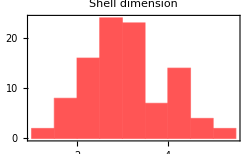
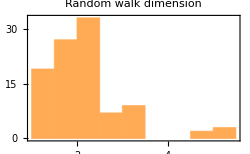

```mathematica
Row[{Histogram[dimvalues2b,PlotTheme->"Web",ChartStyle->Lighter[Red],ImageSize->250,PlotLabel->"Shell dimension"],"    ",Histogram[dimvalues3b,PlotTheme->"Web",ChartStyle->Lighter[Orange],ImageSize->250,PlotLabel->"Random walk dimension"]}]
```

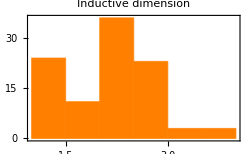
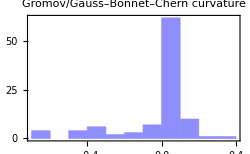

```mathematica
Row[{Histogram[dimvalues4b,PlotTheme->"Web",ChartStyle->Orange,ImageSize->250,PlotLabel->"Inductive dimension"],"    ",Histogram[curvaturesb,PlotTheme->"Web",ChartStyle->Lighter@Lighter@Blue,ImageSize->250,PlotLabel->"Gromov/Gauss–Bonnet–Chern curvature"]}]
```

Distribution of dimensions

```mathematica
rsample=RandomInteger[{0,1645074-1},100];
```

```mathematica
Dynamic[m]
```

```mathematica
dimvalues=Table[N@Last@AssymptoticShellDimension[Last@CreateCSSeriesTrinetReplacement[m,50]],{m,rsample}];
```

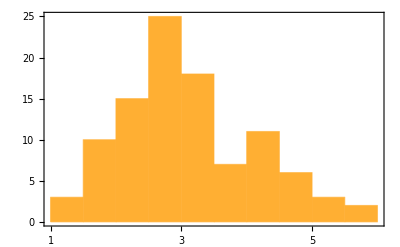

```mathematica
Histogram[dimvalues,10,PlotTheme->"Web",Frame->True]
```

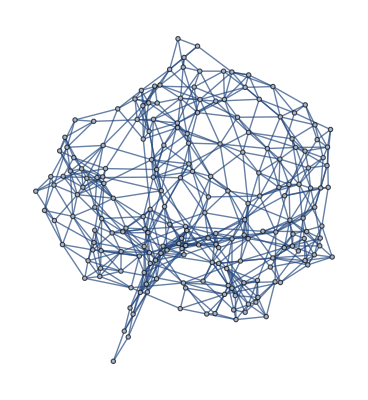
```mathematica
N@AssymptoticShellDimension[-Graphics-,2]
```

{6.87562,6.87562,6.87562,6.87562,6.83756,6.83756,6.35766,5.32353,5.32353}

```mathematica
N@ShellDimension[AdjacencyGraph[AdjacencyMatrix[Last@CreateCSSeriesTrinetReplacement[1289160,200]]]]
```

5.

```mathematica
Last@CreateCSSeriesTrinetReplacement[1289160,200]
```

-Graphics-

```mathematica
Dynamic[m]
```

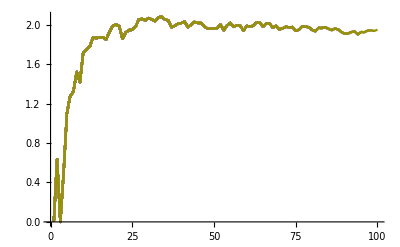

```mathematica
ListLinePlot[Table[N/@Entropy/@VertexDegree/@CreateCSSeriesTrinetReplacement[1289160,m],{m,100}]]
```

The trinet replacement and Turing-based generating networks have extremely similar behaviour, which is on the one hand not completely surprising as both are computational universal and thus are not only capable of fully emulating each other  each other but have also to distribute patterns alike according to Levin’s universal distribution. However, their enumeration may have led to transitional different behaviour before converging, but this is not the case and both models converge very soon yielding similar statistics and therefore stable estimations of entropy and complexity.

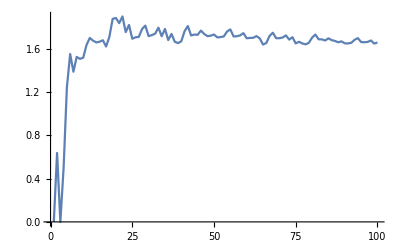

```mathematica
ListLinePlot[N/@Entropy/@VertexDegree/@Table[GenerateCausalSets[1308615,m],{m,100}]]
```

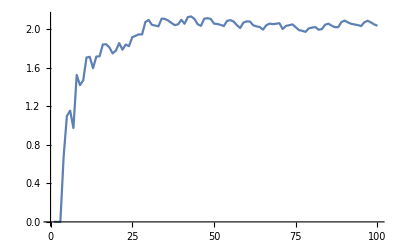

```mathematica
ListLinePlot[N/@Entropy/@VertexDegree/@Table[GenerateCausalSets[38488,m],{m,100}]]
```

```mathematica
ShellDimension/@Table[AdjacencyGraph[Last@CreateTruningCSTimeSeries[m,8,2,200]],{m,randTMs2}]
```

{3,3,3,4,3,3,3,3,3,3,4,4,3,3,3,3,3,3,3,4,3,4,4,4,4,3,3,4,3,3,3,3,4,4,2,4,3,3,4,2,3,3,3,3,3,4,3,3,3,3}